## Stochastic individual - based plasticity experiment

Austin Ferguson

#### Constant Definitions

```mathematica
(* This were changed for the different treatments *)
m = 0.22; (* Per capita death rate of predator *)
kScale = 0.1; (* k = scaling factor for cost of plasticty for prey *)
s = 10; (* Habitat sensitivity of predator *)
(* These *always* stay the same *)
r = {0.9, 0.9};  (* r[i] = intrinsic growth rate of prey y *)
b = {1.0, 1.0}; (* b[i] = per capita birth rate of species i *)
d = {0.1, 0.1}; (* d[i] = per capita death rate of species i *)
k = {2333, 2333}; (* k[i] = carrying capacity of species i *)
aHat= {0.004, 0.004}; (* aHat[i] = maximal predator response of the predator on prey i *)
hHat = {0.4, 0.4}; (* hHat[i] = minimal handling time at the optimal phenotype for prey i *)
cHat = {0.6, 0.2}; (* cHat[i] = Predator's maximal converstion efficiency for prey i *)
uHat = {-1, 1}; (* uHat[i] is the optimal phenotype for habitat i*)
muX = 0.01; (* Mutation probability for x *)
muY = 0.01;(* Mutation probability for y *)
sigmaX =0.1;(* Width of normal distribution for mutation size *)
sigmaY =0.1; (* Width of normal distribution for mutation size *)
sigmaA = 1; (* Used in calcuation of a *)
sigmaASquared = sigmaA * sigmaA; (* Variance of a *)
sigmaH = 1; (* Used in calculation of h *)
sigmaHSquared = sigmaH * sigmaH;   (* Variance of h *)
```

Null

#### Variable Definitions

```mathematica
n = {500,500};
popSize= 500;
numUpdates = 10000;
maxTime = 10000;
printStep = 100;
```

#### Function Definitions

```mathematica
bound[x_]:= Max[Min[x, 1], -1]
```

```mathematica
phenotype[g_] := {bound[g[[1]] - g[[2]]], bound[g[[1]] + g[[2]]]}
a[i_, g_] := aHat[[i]] * Exp[-1 * ( (uHat[[i]] - phenotype[g][[i]])^2 ) / (2 * sigmaASquared)];
h[i_, g_] := hHat[[i]] + (1 - Exp[  -1 * (uHat[[i]] - phenotype[g][[i]] )^2 / (2 * sigmaHSquared )]);
f[i_, g_] := (a[i, g] * n[[i]]) / (1 + a[i, g] * h[i, g] * n[[i]]);
c[i_, g_] := cHat[[i]] * (1 - phenotype[g][[2]] * kScale)
qHelper[i_, g_] := (c[i, g] * f[i, g]) / m;
q[g_] := 1 / (1 + Exp[-1 * s * (qHelper[1, g] - qHelper[2,g])]);
forageRate1[q_, g_] := q * f[1, g];
forageRate2[q_, g_] := (1-q) * f[2, g];
(*nStep[i_, u_] := r[[i]] * n[[i]](1 - (n[[i]] / k[[i]])) - forageRate1[q[1, u], u] * p ;*)
pStep[g_] := p *(c[1, g]*forageRate1[q[g], g] + c[2, g] * forageRate2[q[g], g])  - m * p;
```

#### Basic tests

```mathematica
genotype = {0,1};
phenotype[genotype]
```

{-1,1}

```mathematica
pStep[genotype]
```

0.281468

```mathematica
q[genotype]
```

1.

```mathematica
a[1, genotype]
a[2,genotype]
```

0.004

0.004

```mathematica
h[1,genotype]
h[2,genotype]
```

0.4

0.4

```mathematica
f[1, genotype]
```

1.11111

```mathematica
c[1, genotype]
```

0.54

```mathematica
qHelper[1,genotype]
qHelper[2,genotype]
```

2.72727

0.909091

```mathematica
foo = {1, 2, 3}
```

{1,2,3}

#### Initialization

Create the population vector, where each individual in the population is another two - element vector

```mathematica
pop = {};
xDist= NormalDistribution[0,  0.05];
yDist= NormalDistribution[0,  0.05];
For[i= 1 , i ≤ popSize, i++, 
y = RandomVariate[yDist];
While[y < 0; y = RandomVariate[yDist]];
pop = Append[pop, {RandomVariate[xDist],y}];
];
pop
```

{{0.0325345,-0.00630276},{0.0343137,0.0275972},{0.00758919,0.0670266},{0.0174842,-0.0662504},{0.158107,-0.0107161},{-0.0278776,0.0166596},{0.0349386,-0.0963543},{-0.0286444,-0.0839714},{0.040486,0.083601},{-0.00957947,-0.0702035},{-0.071204,-0.0199164},{0.0198424,0.0643543},{-0.0396736,0.0243272},{0.0524541,0.0120931},{0.0668057,-0.00781008},{-0.00318736,-0.049603},{0.061744,0.0162854},{-0.0316258,0.132041},{-0.00683721,-0.0136021},{-0.0508103,0.0563877},{0.0340623,-0.000381935},{0.153871,0.00432485},{-0.0435176,0.0274775},{0.0753588,-0.0566096},{0.0485554,0.0549834},{0.0763639,0.0237873},{0.0254963,0.00602281},{-0.0674766,-0.0967926},{-0.0973872,-0.096928},{-0.0500407,0.0661959},{-0.0304167,0.00770089},{0.025536,0.0149344},{0.030771,-0.0473788},{-0.026471,0.0569144},{0.00350731,-0.0423595},{-0.0419391,-0.0230724},{-0.0850141,0.015922},{0.0506478,-0.00790309},{0.00331972,0.00878486},{-0.00583084,-0.0239449},{0.0400272,0.0189707},{0.0619071,-0.0441392},{-0.0387946,-0.00279364},{-0.00178007,-0.0212873},{0.00833884,-0.0421523},{0.050158,-0.00315615},{0.00971057,-0.0694581},{-0.006038,0.0255502},{-0.0759075,0.0403491},{0.118927,0.0214351},{0.011479,-0.0570449},{0.0970359,0.0630911},{0.0482826,0.0197681},{-0.0742054,0.0143986},{0.0468397,-0.0489168},{-0.0293521,-0.0217637},{0.0822201,-0.0105495},{0.0505807,0.0720299},{0.0574901,0.0668126},{-0.0940556,-0.026238},{-0.0515309,-0.077538},{-0.0160483,-0.00344973},{-0.0444119,-0.00462592},{0.0746684,0.00415357},{-0.0366581,-0.0124373},{0.00893558,0.0688952},{0.0730172,-0.020595},{-0.0475039,-0.0288778},{0.0661741,-0.0378377},{-0.0413223,0.0781033},{-0.000642645,-0.0408213},{-0.0430467,-0.0716222},{0.119989,-0.0405825},{-0.0481218,0.00140037},{-0.0259565,0.0318437},{0.0142558,-0.018045},{0.0923556,0.0347825},{0.00511172,0.0512179},{0.0889996,-0.0400776},{-0.0871192,0.11337},{0.00853862,-0.0167895},{-0.0684154,-0.0107509},{-0.0498735,0.0106018},{0.0238344,-0.0308723},{0.0526899,-0.0761923},{-0.0223063,-0.0408741},{-0.0101127,-0.0238423},{-0.0364113,-0.0168176},{0.0226914,-0.0277303},{0.0773941,0.001819},{-0.0682532,-0.0120603},{-0.001807,0.0316506},{0.128711,-0.030963},{-0.0227843,-0.0864868},{-0.0271385,0.0512968},{0.0190096,0.0527838},{0.0300701,-0.0171546},{-0.0108687,-0.0103129},{0.0477211,0.0485391},{-0.0156228,-0.00342942},{0.0656412,-0.0318292},{-3.72641×10^-6,0.0830113},{-0.0618646,-0.0353765},{-0.00241041,0.0793816},{0.0427692,0.0777293},{0.00155157,0.0161994},{-0.0377646,0.10012},{-0.0285683,-0.0202997},{0.0375516,-0.021843},{0.0578144,-0.00339136},{-0.112112,-0.0796034},{0.0134341,-0.025804},{-0.11123,0.0973627},{-0.0210537,0.0308413},{-0.0681033,0.0118163},{-0.0409402,-0.00884962},{-0.0540337,-0.0270793},{0.113958,-0.021086},{0.032684,-0.0119992},{0.133175,0.0210971},{-0.00035975,0.0112896},{-0.0195807,0.0453202},{-0.0507474,0.11411},{0.0287309,-0.0276715},{-0.00287602,-0.0672979},{-0.0729951,-0.0795676},{0.0447636,0.0471984},{-0.063521,0.0346579},{0.0462753,0.0941242},{0.00971439,-0.0373902},{-0.0243256,0.0815499},{-0.0469525,0.000705221},{0.0186481,-0.0571974},{0.0669284,-0.0210617},{0.0177442,-0.0790367},{-0.0377232,-0.00368733},{0.019583,0.0258952},{0.019517,0.0177904},{-0.0151736,-0.0603905},{0.0924565,-0.0157575},{0.00782934,0.0157784},{0.0226027,-0.077395},{-0.0149316,-0.0728456},{-0.0445497,0.0426843},{-0.0373803,0.0130332},{-0.0985824,-0.00996926},{-0.000446739,0.00830983},{-0.00781238,0.0646796},{0.0330793,0.0050138},{0.0070175,-0.0171416},{0.00915282,0.105255},{-0.0157029,-0.0230124},{-0.0467894,-0.0467637},{-0.0208601,-0.0411149},{0.0398313,-0.035599},{-0.0253296,-0.016727},{-0.032341,0.0566686},{-0.0943856,0.0547836},{0.0945251,-0.0559271},{0.0101098,0.0556416},{-0.0272648,0.0804114},{-0.0213175,-0.0232334},{0.0181659,0.0640432},{-0.0138042,0.109585},{0.00896681,-0.0317934},{0.0702107,-0.0658525},{-0.0215001,-0.00764987},{-0.00483363,0.015224},{0.0264987,-0.0689896},{-0.0503498,0.0168413},{-0.0574325,0.107016},{0.0053221,-0.0651967},{0.0410771,0.00428557},{0.0264776,0.0412065},{0.0266674,-0.00551554},{0.0797506,0.0263195},{0.138551,0.000688673},{-0.00242461,0.0570023},{0.0176748,0.00691773},{0.0615619,0.0145723},{0.0183443,-0.0305492},{0.10389,0.0359701},{-0.0216442,-0.0298474},{0.059297,0.00506007},{0.0110693,0.0112151},{0.0139467,-0.0256347},{0.0584962,-0.0521434},{0.0425301,-0.0404238},{-0.0548625,0.0838517},{-0.0862525,-0.0374865},{0.0197232,-0.0510512},{-0.025064,0.10341},{-0.0409333,-0.0183117},{-0.00121854,-0.0325436},{0.0255721,-0.108213},{0.0416207,0.0344259},{-0.0746033,-0.0782076},{0.0317938,0.0401419},{-0.0122915,0.0072882},{0.0311207,0.0747127},{-0.042418,0.0133177},{0.01736,0.00193785},{-0.0826868,-0.00357756},{0.109072,-0.0363088},{-0.059131,-0.0441389},{-0.0160942,-0.0216613},{-0.0145257,0.0382006},{-0.0611044,-0.0365217},{0.055779,0.122161},{-0.000336951,0.0079037},{-0.0227466,0.0349219},{-0.0451624,-0.0850671},{0.0624057,0.0154844},{-0.01914,0.0285111},{0.0558325,0.0495141},{-0.0243086,-0.0220549},{0.0460805,0.023852},{0.0504812,0.00814191},{-0.0609708,0.0417916},{0.0247143,0.107525},{-0.0281049,0.0122498},{-0.0380047,-0.135603},{0.0194078,0.0983776},{0.0243545,0.00896513},{-0.0454735,0.075415},{0.0718782,0.0335736},{-0.0150239,-0.0487593},{-0.0349507,-0.0413341},{-0.0364825,0.000745146},{-0.0700028,0.0541154},{-0.0289004,0.0593014},{-0.0591922,-0.0209655},{0.0166837,-0.0513729},{0.0177017,-0.0252458},{0.0797185,-0.0710623},{-0.0408947,-0.0517128},{0.000174217,-0.0232633},{-0.0574586,-0.0520377},{0.0752177,-0.0421981},{-0.0206816,0.0910676},{0.013998,-0.0511217},{0.0173846,-0.0492031},{0.0324895,-0.0317733},{0.00719101,-0.0175745},{-0.0123417,0.0270486},{-0.0124606,-0.0535643},{0.0506915,-0.0258184},{0.0124782,0.0208125},{-0.0698357,0.0544237},{0.000636413,-0.036259},{0.0599016,-0.0230968},{-0.073568,-0.000761871},{0.000413234,-0.0863348},{0.0109477,0.0163381},{-0.0437201,0.062005},{-0.129925,-0.0369516},{-0.0181056,0.0276504},{-0.0112568,-0.0656314},{-0.0508,0.0752893},{-0.0671801,-0.0436997},{-0.0410264,0.0762392},{0.0722319,-0.0549385},{0.0222765,-0.00774952},{-0.00168878,0.00888941},{0.0140483,0.0380855},{0.029371,0.0292979},{-0.0941312,0.0867405},{0.00713527,-0.0353448},{-0.0900215,0.0311461},{0.0776881,0.0975794},{-0.00673936,0.0024687},{0.0884907,-0.031744},{-0.0283888,0.01077},{0.0249938,-0.0563905},{0.0371064,0.00847327},{-0.010202,-0.0382358},{-0.0282733,0.0567972},{0.0072273,-0.0193832},{-0.0634864,-0.0683726},{0.0340359,-0.017078},{-0.120052,-0.0812757},{-0.00246784,0.019308},{0.103969,-0.0778546},{0.0307023,-0.105055},{0.111975,0.0501464},{0.0207404,-0.0100503},{-0.0729523,-0.0531392},{0.0190549,-0.0257347},{0.0711867,-0.0145509},{0.0290684,-0.0277734},{0.0263698,-0.041052},{-0.00517446,0.0211994},{-0.0302288,-0.00537015},{0.029472,-0.0560857},{0.0180437,-0.0193821},{-0.0614802,-0.0426377},{0.0237714,-0.0693677},{0.0807171,0.0508659},{0.0172158,0.0138176},{-0.0402767,-0.059163},{-0.0848845,0.0229047},{0.000855866,0.0636291},{0.0318884,-0.0849134},{-0.00207156,-0.0551941},{-0.0318942,-0.0372606},{-0.0185917,0.0294147},{0.0260425,0.0252192},{-0.03246,-0.0228539},{-0.0674872,-0.0134295},{-0.0332503,-0.01437},{0.0741112,-0.0295835},{-0.0303669,-0.0142783},{-0.0100299,0.000532875},{-0.013127,-0.0421497},{0.022089,-0.00628628},{-0.00120229,-0.057624},{-0.0443903,-0.0781339},{-0.0641654,0.0540061},{0.0104968,-0.0140952},{0.0936227,-0.0127324},{0.0262679,-0.0252009},{0.0958116,0.00653},{-0.0604258,-0.0200086},{-0.0182065,0.0132937},{0.0786668,0.00325943},{-0.035659,0.0120294},{0.0690617,0.0514493},{0.000110357,0.0142463},{-0.0263264,-0.0523738},{-0.0622564,0.027412},{-0.0271769,-0.00885472},{0.0023055,0.0169148},{-0.0141913,-0.0990201},{-0.00818357,-0.0644418},{0.0662347,-0.0392796},{0.0172976,0.0445409},{-0.0444307,0.0427876},{0.0397651,-0.00197786},{0.0345437,-0.108903},{-0.0740759,0.0381024},{0.00441993,-0.0915397},{-0.0789802,-0.00248223},{-0.0684468,-0.00918744},{0.0404342,0.0743304},{-0.0475493,0.0450009},{0.0214691,0.0254833},{0.000640042,0.0089161},{0.0197775,-0.0708051},{-0.086865,-0.0219927},{0.0185055,0.0113025},{-0.0379031,-0.0554632},{0.00318153,0.0502017},{-0.0414184,0.0334215},{-0.0643853,0.0271973},{-0.0519917,0.0366177},{0.0608751,-0.0241844},{-0.00660736,0.00237415},{0.0388789,0.0177252},{0.0527207,-0.0774962},{-0.0924632,-0.0181057},{0.0606168,-0.0833372},{-0.0151616,0.0127837},{-0.0430095,-0.0631325},{0.000264203,-0.0150421},{0.043182,-0.0723815},{-0.0767704,0.0315211},{-0.00220994,-0.0047342},{-0.0766341,0.124923},{0.00542294,-0.0124467},{-0.0134559,0.0985492},{0.0293774,-0.00977583},{-0.0786499,-0.027753},{-0.0412848,0.0301341},{-0.0371372,-0.0437675},{0.0627383,-0.0379565},{0.0416603,0.0694597},{0.108515,0.0707319},{-0.00358254,0.0106666},{0.0794324,-0.0510869},{-0.124537,0.015767},{0.0125082,-0.0647933},{-0.109076,0.00889082},{-0.0715584,0.0247483},{-0.00626164,-0.0124434},{-0.0440957,-0.0298404},{-0.0862755,0.00231753},{-0.0485007,-0.0434161},{0.0574715,-0.0446421},{-0.0485129,-0.00304674},{0.0564739,0.0179912},{0.0397429,0.00805183},{-0.016763,0.0550743},{0.029146,0.0648822},{-0.0130322,0.0332127},{0.0258548,-0.0606243},{-0.0716046,-0.056945},{0.0318881,0.00820329},{0.00783348,-0.0542519},{0.00586384,0.0181522},{0.0323371,-0.0395962},{0.0420539,-0.0259824},{-0.00776978,0.0636882},{-0.00327939,-0.000164793},{-0.00132172,-0.0769784},{0.0297746,0.0117825},{0.0240222,-0.0196511},{0.0118112,-0.059235},{-0.0213379,-0.00651203},{-0.0409914,0.0610793},{0.00647293,-0.0351943},{0.0328902,-0.0611383},{-0.00994918,-0.042141},{-0.074768,0.0913981},{0.00619726,0.0173311},{-0.022262,-0.0096777},{-0.0276858,0.00546597},{-0.0330757,-0.0233926},{0.0466202,-0.0170049},{-0.0453768,-0.0468582},{0.0859726,-0.00905007},{-0.0468477,0.0209216},{0.0871281,0.012882},{-0.00303327,-0.108392},{0.0428844,0.0142576},{0.0559393,0.00135531},{0.00717851,-0.0278034},{-0.0666364,-0.0716776},{0.0720126,-0.0081335},{-0.0201766,0.0326374},{0.0943449,0.0508799},{-0.0581534,-0.00140259},{0.0618312,0.014285},{0.0404091,0.00252387},{-0.0171768,0.12663},{0.0801564,0.0794241},{0.0764344,-0.0555863},{0.0767582,0.00628525},{0.0737606,-0.0785655},{-0.112994,0.0287824},{-0.023688,-0.0159198},{0.0474352,0.0247385},{-0.0260458,-0.0696297},{0.0297817,-0.0254981},{-0.0589077,0.0250706},{0.0562142,-0.0455552},{-0.0412642,-0.0268627},{-0.0573243,-0.0328276},{0.0590756,0.0344307},{-0.0179256,0.0326605},{0.0325064,0.0575757},{-0.0606808,-0.0289733},{-0.0610345,-0.00419231},{-0.0395065,-0.0915611},{0.0926714,0.0453773},{0.059753,0.00817873},{0.050409,-0.0802637},{0.0387557,-0.0878165},{0.0423408,0.105773},{-0.00858557,-0.0386611},{-0.0426878,0.0797052},{-0.0278372,-0.0720318},{-0.0182129,0.0120986},{0.0304454,0.0609152},{0.0419097,-0.0227519},{0.0241452,0.0294771},{-0.0561756,-0.00756679},{0.0162706,-0.0235764},{-0.0511377,0.106903},{0.0600259,-0.00242742},{0.0114667,0.01431},{0.0765598,0.0100983},{0.0851643,-0.0494591},{0.0137719,0.0388711},{0.011806,0.0582248},{-0.0411581,0.00585951},{0.00179481,-0.0238107},{0.0984612,0.0377871},{0.0557368,0.0567805},{-0.0215805,-0.0227591},{-0.0608757,-0.0705803},{-0.0629424,0.0228672},{-0.0284512,-0.0659278},{-0.0695742,-0.0287391},{-0.0271746,-0.00381716},{0.0159129,0.0279746},{0.0462865,-0.0925504},{-0.0313243,0.053958},{0.0973936,-0.0152985},{0.0310102,0.0726807},{0.0291927,-0.0288833},{-0.0152194,0.0000941249},{-0.0821582,0.00784647},{-0.0475493,0.110558},{0.038555,0.0401093},{0.0365154,-0.0916858},{-0.100053,0.0604018},{-0.0987815,-0.0836029},{-0.0727632,-0.0548277},{0.00778205,-0.071333},{-0.0377281,0.0589654}}

#### Main Loop

```mathematica
qArr = ConstantArray[0, popSize];
forageRate1Arr = ConstantArray[0, popSize];
forageRate2Arr = ConstantArray[0, popSize];
c1Arr = ConstantArray[0, popSize]; 
c2Arr = ConstantArray[0, popSize]; 
bArr = {};
historyPred = ConstantArray[0, numUpdates];
historyPrey1 = ConstantArray[0, numUpdates];
historyPrey2 = ConstantArray[0, numUpdates];
update = 0;
timeElapsed = 0;
(*For[update = 1, update <= numUpdates, update++,*)
While[timeElapsed < maxTime,
update++;
historyPred[[update]] = Length[pop];
historyPrey1[[update]] = n[[1]];
historyPrey2[[update]] = n[[2]];
For[j = 1, j <= Length[pop], j++,
genotype = pop[[j]];
qArr[[j]]=q[genotype];
forageRate1Arr[[j]] = forageRate1[qArr[[j]], genotype];
forageRate2Arr[[j]] = forageRate2[qArr[[j]], genotype];
c1Arr[[j]] = c[1, genotype];
c2Arr[[j]] = c[2, genotype];
];
b1 = r[[1]]*n[[1]];
b2 = r[[2]]*n[[2]];
d1 = (r[[1]]* (n[[1]]^2) / k[[1]])+Total[forageRate1Arr];
d2 = (r[[2]]* (n[[2]]^2) / k[[2]])+Total[forageRate2Arr];
bArr = c1Arr * forageRate1Arr + c2Arr * forageRate2Arr;
bP = Total[bArr];
dP = m * Length[pop];
total = b1 + b2 + d1 + d2 + bP + dP;
timeElapsed += RandomVariate[ExponentialDistribution[total]];
(*Print[b1, " + ", b2, " + ", d1, " + ", d2, " + ", bP, " + ", dP, " = ", total];*)
(*Print[b1/total, " + ", b2/total, " + ", d1/total, " + ", d2/total, " + ", bP/total, " + ", dP/total, " = ", total/total];*)
p = RandomReal[];
If[Mod[update, printStep] == 0,Print["update:", update, "; pop size: ", Length[pop], "; elapsed time: ", timeElapsed];,];If[p ≤ b1 / total, (*Print["Birth prey 1"];*)n[[1]]++;Continue[]; ];
If[p ≤ (b2 + b1) / total, (*Print["Birth prey 2"];*)n[[2]]++;Continue[]; ];
If[p ≤  (d1 + b2 + b1) / total, (*Print["Death prey 1"];*)n[[1]]--; Continue[]; ];
If[p ≤  (d2 + d1 + b2 + b1) / total, (*Print["Death prey 2"];*)n[[2]]--; Continue[]; ];
If[p ≤  (bP + d2 + d1 + b2 + b1) / total,        
bIdx = RandomChoice[bArr / Total[bArr]-> Range[1, Length[pop]]];
(*Print["Birth predator ", bIdx];*)
org = pop[[bIdx]];
x = org[[1]];
y = org[[2]];
If[RandomReal[] < muX,
x= RandomVariate[NormalDistribution[org[[1]],sigmaX]]
];
If[RandomReal[] < muX,
y= RandomVariate[NormalDistribution[org[[2]],sigmaY]];
While[y < 0, y = RandomVariate[NormalDistribution[org[[2]],sigmaY]];];
];
newOrg = {x,y};
(*Print["org: ", org, "New org: ", newOrg];*)
pop = Append[pop, newOrg];
qArr = Append[qArr, 0];
forageRate1Arr = Append[forageRate1Arr, 0];
forageRate2Arr = Append[forageRate2Arr, 0];
c1Arr = Append[c1Arr,0];
c2Arr = Append[c2Arr,0];
bArr = Append[bArr,0];
Continue[];
];
If[p≤  (dP + bP + d2 + d1 + b2 + b1) / total, 
dIdx = RandomInteger[{1, Length[pop]}];
(*Print["Death predator ", dIdx];*)
pop = Delete[pop, dIdx];
qArr = Delete[qArr, dIdx];
forageRate1Arr = Delete[forageRate1Arr, dIdx];
forageRate2Arr = Delete[forageRate2Arr, dIdx];
c1Arr = Delete[c1Arr, dIdx];
c2Arr = Delete[c2Arr, dIdx];
bArr = Delete[bArr, dIdx];
Continue[];
];
];
```

update:100; pop size: 503; elapsed time: 0.0541451

update:200; pop size: 512; elapsed time: 0.10559

update:300; pop size: 514; elapsed time: 0.162556

$Aborted

#### Plots

Plots

Populations over time

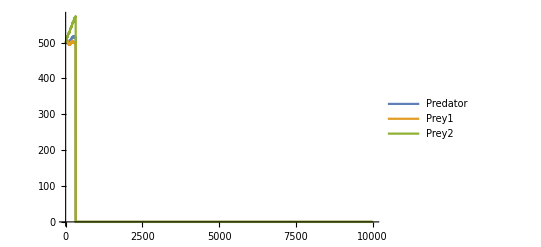

```mathematica
ListLinePlot[{historyPred, historyPrey1, historyPrey2}, PlotLegends-> {"Predator", "Prey1", "Prey2"}]
```

Population at end of evaluation

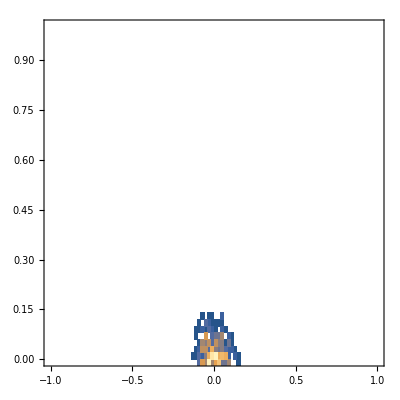

```mathematica
DensityHistogram[pop, PlotRange->{{-1,1},{0,1}}]
```